```mathematica
SetDirectory[NotebookDirectory[]];
Get["../source/mathematica/AnalyticValence.wl"];
Get["../source/mathematica/FigureSettings.wl"];
InitializePlotSettings[]
```

```mathematica
{IP,IN,r,V,ϵ1,ϵ2}={1,1,2,1,0.2,0.01};
II=(IP+IN)/(1+r);
J=(IP-r*IN)/(2*(1+r));
```

Analytic results:

```mathematica
{ϕ1,p1,n1}=r2Results[J,II,V,ϵ1];
{ϕ2,p2,n2}=r2Results[J,II,V,ϵ2];
```

```mathematica
pFuncs=(#[x]&)/@{p1,p2};
nFuncs=(#[x]&)/@{n1,n2};
phiFuncs=(#[x]&)/@{ϕ1,ϕ2};
```

```mathematica
pPlot=Plot[pFuncs,{x,0,1},PlotRange->{{0,1},{0.3,1.8}},PlotStyle->{Directive[NumCompColours[[3]],Dashing[{0.02,0.03}],Thickness[0.01]],Directive[NumCompColours[[4]],Dashing[{0.02,0.03}],Thickness[0.01]]},Frame->True,AspectRatio->1,ImageSize->400];nPlot=Plot[nFuncs,{x,0,1},PlotRange->{{0,1},{0.3,1.8}},PlotStyle->{Directive[NumCompColours[[3]],Dashing[{0.02,0.03}],Thickness[0.01]],Directive[NumCompColours[[4]],Dashing[{0.02,0.03}],Thickness[0.01]]},Frame->True,AspectRatio->1,GridLines->Automatic,ImageSize->400];ϕPlot=Plot[phiFuncs,{x,0,1},PlotRange-> {{0,1},{0,1}},PlotStyle->{Directive[NumCompColours[[3]],Dashing[{0.02,0.03}],Thickness[0.01]],Directive[NumCompColours[[4]],Dashing[{0.02,0.03}],Thickness[0.01]]},Frame->True,AspectRatio->1,ImageSize->400];
```

Numerical results:

```mathematica
dataNum1=Import[FileNameJoin[{NotebookDirectory[],"..","data","pnp_zp2_zn1_Ip1.00_In1.00_eps0.200.csv"}],"CSV"];
{xNum1,pNum1,nNum1,ϕNum1}=Transpose[dataNum1[[2;;]]];
```

```mathematica
dataNum2=Import[FileNameJoin[{NotebookDirectory[],"..","data","pnp_zp2_zn1_Ip1.00_In1.00_eps0.010.csv"}],"CSV"];
{xNum2,pNum2,nNum2,ϕNum2}=Transpose[dataNum2[[2;;]]];
```

```mathematica
pNum={pNum1,pNum2};
nNum={nNum1,nNum2};
phiNum={ϕNum1,ϕNum2};
```

```mathematica
NumericalPlotP=ListLinePlot[{Transpose[{xNum1,pNum1}],Transpose[{xNum2,pNum2}]},PlotRange->{{0,1},{0.5,1.6}},AspectRatio->1,ImageSize->Large,PlotStyle->{Directive[NumCompColours[[1]],Thickness[0.012]],Directive[NumCompColours[[2]],Thickness[0.012]]}];NumericalPlotN=ListLinePlot[{Transpose[{xNum1,nNum1}],Transpose[{xNum2,nNum2}]},PlotRange->{{0,1},{0.8,1.2}},AspectRatio->1,ImageSize->Large,PlotStyle->{Directive[NumCompColours[[1]],Thickness[0.012]],Directive[NumCompColours[[2]],Thickness[0.012]]},FrameTicks->{{{{0.8,"0.8"},{0.9,"0.9"},{1.0,"1.0"},{1.1,"1.1"},{1.2,"1.2"}},None},{Automatic,None}}];NumericalPlotϕ=ListLinePlot[{Transpose[{xNum1,ϕNum1}],Transpose[{xNum2,ϕNum2}]},PlotRange->{{0,1},{0,1}},AspectRatio->1,ImageSize->Large,PlotStyle->{Directive[NumCompColours[[1]],Thickness[0.012]],Directive[NumCompColours[[2]],Thickness[0.012]]}];
```

Combined Plots

```mathematica
PPlotEps=Show[NumericalPlotP,pPlot];
```

```mathematica
NPlotEps=Show[NumericalPlotN,nPlot];
```

```mathematica
ϕPlotEps=Show[NumericalPlotϕ,ϕPlot];
```

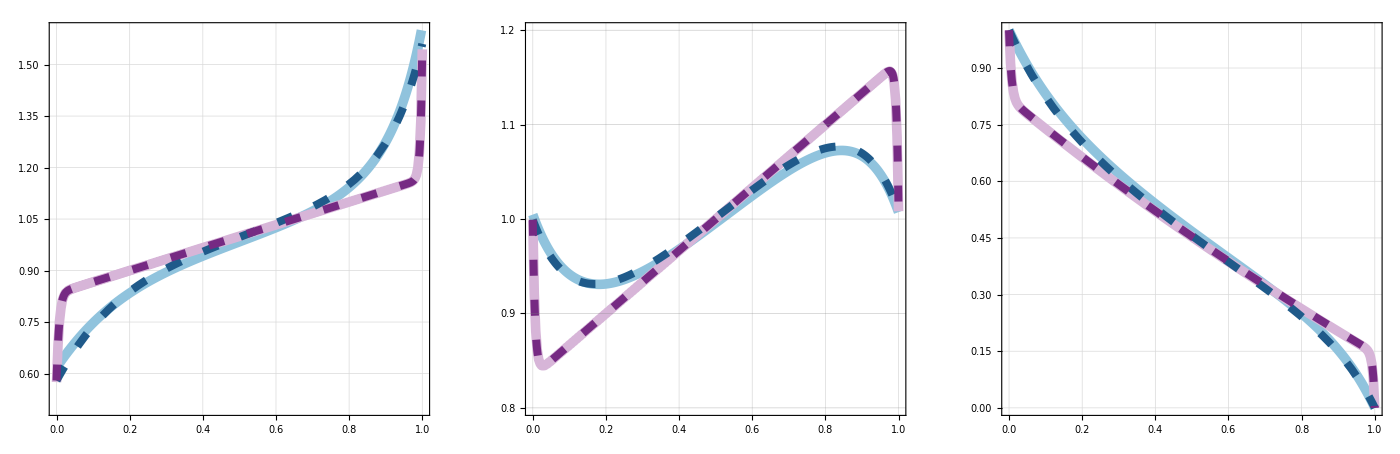

```mathematica
triptychNumerical=GraphicsRow[{PPlotEps,NPlotEps,ϕPlotEps},Spacings->30,ImageSize->1400]
```

Labels and annotations added in photo editing software Canva.

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"..","figures","Figure3.pdf"}],triptychNumerical,ImageResolution->300]
```

/Users/georginaryan/Desktop/DPhil/Research/Draft Papers/Journal Article - Chapter 4/Figures Ratio Version/Final Code for Repository/asymmetric-valence-electrolytes/notebooks/../figures/Figure3.pdf